```mathematica
ρ3pF0[r_]:= (1 + w r^2/c^2)Exp[-(r-c)/z]/(1 + Exp[-(r-c)/z]);
Subscript[ρ, 03]=4Pi Integrate[r^2 ρ3pF0[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}];
ρ3pF[r_]:= (Z/Subscript[ρ, 03])*(1 + w r^2/c^2)/(1 + Exp[(r-c)/z]);(* *Z !  *)
Plot[82*ρ3pF[r]/.{c->6.4,z->0.54,w->0.32},{r,0,10}]
```

-Graphics-

```mathematica
4 Pi Integrate[r^2 ρ3pF[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}]
```

1

```mathematica
V3pF[r_]:=-4 Pi α*( 1/r Integrate[x^2 ρ3pF[x],{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]+Integrate[x ρ3pF[x],{x,r,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]);
FullSimplify[V3pF[r]]
```

(α (r (c^2+r^2 w) PolyLog[2,-ⅇ^((c-r)/z)]+2 z (-c^2 PolyLog[3,-ⅇ^(c/z)]+(c^2+3 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]+3 w z (3 r PolyLog[4,-ⅇ^((c-r)/z)]-4 z PolyLog[5,-ⅇ^(c/z)]+4 z PolyLog[5,-ⅇ^((c-r)/z)]))))/(2 r z (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

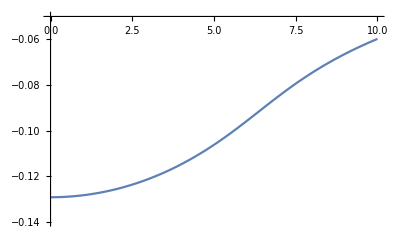

```mathematica
V3pFexpl[r_]:=(α (r (c^2+r^2 w) PolyLog[2,-ⅇ^((c-r)/z)]+2 z (-c^2 PolyLog[3,-ⅇ^(c/z)]+(c^2+3 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]+3 w z (3 r PolyLog[4,-ⅇ^((c-r)/z)]-4 z PolyLog[5,-ⅇ^(c/z)]+4 z PolyLog[5,-ⅇ^((c-r)/z)]))))/(2 r z (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]));
Plot[{82*V3pFexpl[r]/.{α->1/137.035999177,c->6.4,z->0.54,w->0.32}},{r,0,10},PlotRange->{-0.14,-0.05}]
```

```mathematica
V3pF0[r_]:=-4 Pi α*( 1/r Integrate[x^2 ρ3pF0[x],{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]+Integrate[x ρ3pF0[x],{x,r,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]);
FullSimplify[V3pF0[r]]
```

-1/(c^2 r)4 π z^2 α (r (c^2+r^2 w) PolyLog[2,-ⅇ^((c-r)/z)]+2 z (-c^2 PolyLog[3,-ⅇ^(c/z)]+(c^2+3 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]+3 w z (3 r PolyLog[4,-ⅇ^((c-r)/z)]-4 z PolyLog[5,-ⅇ^(c/z)]+4 z PolyLog[5,-ⅇ^((c-r)/z)])))

```mathematica
V3pF0expl[r_]:=-1/(c^2 r)4 π z^2 α (r (c^2+r^2 w) PolyLog[2,-ⅇ^((c-r)/z)]+2 z (-c^2 PolyLog[3,-ⅇ^(c/z)]+(c^2+3 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]+3 w z (3 r PolyLog[4,-ⅇ^((c-r)/z)]-4 z PolyLog[5,-ⅇ^(c/z)]+4 z PolyLog[5,-ⅇ^((c-r)/z)])));
```

```mathematica
V3pF0expl[r]/.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^((c-r)/z)]->Poly2r,PolyLog[3,-ⅇ^((c-r)/z)]->Poly3r,PolyLog[4,-ⅇ^((c-r)/z)]->Poly4r,PolyLog[5,-ⅇ^((c-r)/z)]->Poly5r,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[5,-ⅇ^(c/z)]->Poly5}
```

-(4 π z^2 (Poly2r r (c^2+r^2 w)+2 z (-c^2 Poly3+Poly3r (c^2+3 r^2 w)+3 w z (3 Poly4r r-4 Poly5 z+4 Poly5r z))) α)/(c^2 r)

```mathematica
FortranForm[%35]
```

(-4*Pi*z**2*(Poly2r*r*(c**2 + r**2*w) + 2*z*(-(c**2*Poly3) + Poly3r*(c**2 + 3*r**2*w) + 3*w*z*(3*Poly4r*r - 4*Poly5*z + 4*Poly5r*z)))*α)/
     -  (c**2*r)

```mathematica
Series[V3pF0expl[r],r->0]
```

(4 π z^2 α (c^2 PolyLog[2,-ⅇ^(c/z)]+6 w z^2 PolyLog[4,-ⅇ^(c/z)]))/c^2+O[r]^1

```mathematica
Normal[(4 π z^2 α (c^2 PolyLog[2,-ⅇ^(c/z)]+6 w z^2 PolyLog[4,-ⅇ^(c/z)]))/c^2+O[r]^1]/.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^(c/z)]->Poly2,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[4,-ⅇ^(c/z)]->Poly4,PolyLog[5,-ⅇ^(c/z)]->Poly5}
```

(4 π z^2 (c^2 Poly2+6 Poly4 w z^2) α)/c^2

```mathematica
FortranForm[%43]
```

(4*Pi*z**2*(c**2*Poly2 + 6*Poly4*w*z**2)*α)/c**2

```mathematica
4 Pi Integrate[r^4 ρ3pF0[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}]
```

4 π (-24 z^5 PolyLog[5,-ⅇ^(c/z)]-(720 w z^7 PolyLog[7,-ⅇ^(c/z)])/c^2)

```mathematica
%45 /.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^(c/z)]->Poly2,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[4,-ⅇ^(c/z)]->Poly4,PolyLog[5,-ⅇ^(c/z)]->Poly5,PolyLog[7,-ⅇ^(c/z)]->Poly7}
```

4 π (-24 Poly5 z^5-(720 Poly7 w z^7)/c^2)

```mathematica
FortranForm[%46]
```

4*Pi*(-24*Poly5*z**5 - (720*Poly7*w*z**7)/c**2)

```mathematica
El3pF0[r_]:=(1/r^2)*Integrate[x^2 ρ3pF0[x],{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}];
FullSimplify[El3pF0[r]]
```

1/(c^2 r^2)z (-r^2 (c^2+r^2 w) Log[1+ⅇ^((c-r)/z)]+2 z (r (c^2+2 r^2 w) PolyLog[2,-ⅇ^((c-r)/z)]+z (-c^2 PolyLog[3,-ⅇ^(c/z)]+(c^2+6 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]+12 w z (r PolyLog[4,-ⅇ^((c-r)/z)]-z PolyLog[5,-ⅇ^(c/z)]+z PolyLog[5,-ⅇ^((c-r)/z)]))))

```mathematica
%55/.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^((c-r)/z)]->Poly2r,PolyLog[3,-ⅇ^((c-r)/z)]->Poly3r,PolyLog[4,-ⅇ^((c-r)/z)]->Poly4r,PolyLog[5,-ⅇ^((c-r)/z)]->Poly5r,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[5,-ⅇ^(c/z)]->Poly5}
```

(z (-Poly1r r^2 (c^2+r^2 w)+2 z (Poly2r r (c^2+2 r^2 w)+z (-c^2 Poly3+Poly3r (c^2+6 r^2 w)+12 w z (Poly4r r-Poly5 z+Poly5r z)))))/(c^2 r^2)

```mathematica
FortranForm[%58]
```

(z*(-(Poly1r*r**2*(c**2 + r**2*w)) + 2*z*(Poly2r*r*(c**2 + 2*r**2*w) + 
     -         z*(-(c**2*Poly3) + Poly3r*(c**2 + 6*r**2*w) + 12*w*z*(Poly4r*r - Poly5*z + Poly5r*z)))))/(c**2*r**2)

```mathematica
F3pF0[q_]:=4Pi*Integrate[r^2 SphericalBesselJ[0,r q] ρ3pF0[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,q>=0}];
FullSimplify[F3pF0[q]]
```

-(2 ⅈ ⅇ^(c/z) π z^2 (c^2 (LerchPhi[-ⅇ^(c/z),2,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),2,1+ⅈ q z])+6 w z^2 (LerchPhi[-ⅇ^(c/z),4,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),4,1+ⅈ q z])))/(c^2 q)

```mathematica
FullSimplify[%66/.{LerchPhi[-ⅇ^(c/z),2,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),2,1+ⅈ q z]->-I lp2,LerchPhi[-ⅇ^(c/z),4,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),4,1+ⅈ q z]->-I lp4}]
```

-(2 ⅇ^(c/z) π z^2 (c^2 lp2+6 lp4 w z^2))/(c^2 q)

```mathematica
FortranForm[%68]
```

(-2*E**(c/z)*Pi*z**2*(c**2*lp2 + 6*lp4*w*z**2))/(c**2*q)

```mathematica
ρ2pF0[r_]:= 1/(1 + Exp[(r-c)/z])
ρ3pF0[r_]:= (1 + w r^2/c^2)/(1 + Exp[(r-c)/z])
```

```mathematica
Subscript[ρ, 02]=4Pi Integrate[r^2 ρ2pF0[r],{r,0,Infinity},Assumptions->{z>0,c>0}]
Subscript[ρ, 03]=4Pi Integrate[r^2 ρ3pF0[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}]
```

-8 π z^3 PolyLog[3,-ⅇ^(c/z)]

4 π (-2 z^3 PolyLog[3,-ⅇ^(c/z)]-(24 w z^5 PolyLog[5,-ⅇ^(c/z)])/c^2)

```mathematica
ρ2pF[r_]:= (1/Subscript[ρ, 02])*1/(1 + Exp[(r-c)/z]) (* *Z ?  *)
ρ3pF[r_]:= (1/Subscript[ρ, 03])*(1 + w r^2/c^2)/(1 + Exp[(r-c)/z])  (* *Z ?  *)
```

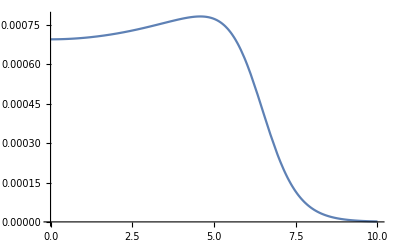

```mathematica
Plot[ρ3pF[r]/.{c->6.4,z->0.54,w->0.32},{r,0,10}]
```

```mathematica
4 Pi Integrate[r^2 ρ2pF[r],{r,0,Infinity},Assumptions->{z>0,c>0}]
4 Pi Integrate[r^2 ρ3pF[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}]
```

1

1

```mathematica
V2pF[r_]:=-4 Pi α*( Integrate[x^2 ρ2pF[x]/r,{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]+Integrate[x ρ2pF[x],{x,r,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]);
V3pF[r_]:=-4 Pi α*( Integrate[x^2 ρ3pF[x]/r,{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]+Integrate[x ρ2pF[x],{x,r,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]);
```

```mathematica
FullSimplify[V2pF[r]]
```

(α (r PolyLog[2,-ⅇ^((c-r)/z)]+2 z (-PolyLog[3,-ⅇ^(c/z)]+PolyLog[3,-ⅇ^((c-r)/z)])))/(2 r z PolyLog[3,-ⅇ^(c/z)])

```mathematica
FullSimplify[V3pF[r]]
```

(α (-2 c^2 z^2 PolyLog[3,-ⅇ^(c/z)]^2+12 r w z^2 (r Log[1+ⅇ^((c-r)/z)]-z PolyLog[2,-ⅇ^((c-r)/z)]) PolyLog[5,-ⅇ^(c/z)]+PolyLog[3,-ⅇ^(c/z)] (-r^4 w Log[1+ⅇ^((c-r)/z)]+r (c^2+4 r^2 w) z PolyLog[2,-ⅇ^((c-r)/z)]+2 (c^2+6 r^2 w) z^2 PolyLog[3,-ⅇ^((c-r)/z)]+24 w z^3 (r PolyLog[4,-ⅇ^((c-r)/z)]+z (-PolyLog[5,-ⅇ^(c/z)]+PolyLog[5,-ⅇ^((c-r)/z)])))))/(2 r z^2 PolyLog[3,-ⅇ^(c/z)] (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
Series[FullSimplify[V3pF[r]],{r,0,2}]
```

-(α PolyLog[2,-ⅇ^(c/z)])/(2 (z PolyLog[3,-ⅇ^(c/z)]))-((ⅇ^(c/z) α (c^2 PolyLog[3,-ⅇ^(c/z)]+36 w z^2 PolyLog[5,-ⅇ^(c/z)])) r^2)/(12 ((1+ⅇ^(c/z)) z^3 PolyLog[3,-ⅇ^(c/z)] (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)])))+O[r]^3

```mathematica
%47/.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^((c-r)/z)]->Poly2r,PolyLog[3,-ⅇ^((c-r)/z)]->Poly3r,PolyLog[4,-ⅇ^((c-r)/z)]->Poly4r,PolyLog[5,-ⅇ^((c-r)/z)]->Poly5r,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[5,-ⅇ^(c/z)]->Poly5}
```

((-2 c^2 Poly3^2 z^2+12 Poly5 r w z^2 (Poly1r r-Poly2r z)+Poly3 (-Poly1r r^4 w+Poly2r r (c^2+4 r^2 w) z+2 Poly3r (c^2+6 r^2 w) z^2+24 w z^3 (Poly4r r+(-Poly5+Poly5r) z))) α)/(2 Poly3 r z^2 (c^2 Poly3+12 Poly5 w z^2))

```mathematica
FortranForm[%50]
```

((-2*c**2*Poly3**2*z**2 + 12*Poly5*r*w*z**2*(Poly1r*r - Poly2r*z) + 
     -      Poly3*(-(Poly1r*r**4*w) + Poly2r*r*(c**2 + 4*r**2*w)*z + 
     -         2*Poly3r*(c**2 + 6*r**2*w)*z**2 + 24*w*z**3*(Poly4r*r + (-Poly5 + Poly5r)*z)))*α)/
     -  (2.*Poly3*r*z**2*(c**2*Poly3 + 12*Poly5*w*z**2))

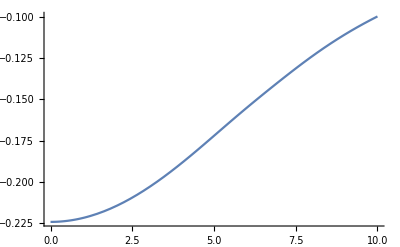

```mathematica
Plot[%13/.{c->6.4,z->0.54,w->0.32},{r,0,10}]
```

```mathematica
FullSimplify[V3pF[r]-V2pF[r]/.{w->0}]
```

0

```mathematica
4 Pi Integrate[r^4 ρ2pF[r],{r,0,Infinity},Assumptions->{z>0,c>0}]
FullSimplify[4 Pi Integrate[r^4 ρ3pF[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity}]]
```

(12 z^2 PolyLog[5,-ⅇ^(c/z)])/PolyLog[3,-ⅇ^(c/z)]

(12 (c^2 z^2 PolyLog[5,-ⅇ^(c/z)]+30 w z^4 PolyLog[7,-ⅇ^(c/z)]))/(c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)])

```mathematica
F2pF[q_]:=4Pi*Integrate[r^2 SphericalBesselJ[0,r q] ρ2pF[r],{r,0,Infinity},Assumptions->{z>0,c>0,q>=0}]
F3pF[q_]:=4Pi*Integrate[r^2 SphericalBesselJ[0,r q] ρ3pF[r],{r,0,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,q>=0}]
```

```mathematica
F2pF[q]
```

(ⅈ ⅇ^(c/z) (LerchPhi[-ⅇ^(c/z),2,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),2,1+ⅈ q z]))/(4 q z PolyLog[3,-ⅇ^(c/z)])

```mathematica
FullSimplify[Re[I ( LerchPhi[-ⅇ^(c/z),2,1-I q z]-LerchPhi[-ⅇ^(c/z),2,1+I q z])]]
```

Im[-LerchPhi[-ⅇ^(c/z),2,1-ⅈ q z]+LerchPhi[-ⅇ^(c/z),2,1+ⅈ q z]]

```mathematica
FullSimplify[F3pF[q]]
```

(ⅈ ⅇ^(c/z) (c^2 (LerchPhi[-ⅇ^(c/z),2,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),2,1+ⅈ q z])+6 w z^2 (LerchPhi[-ⅇ^(c/z),4,1-ⅈ q z]-LerchPhi[-ⅇ^(c/z),4,1+ⅈ q z])))/(4 q z (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
El2pF[r_]:=(1/r^2)*Integrate[x^2 ρ2pF[x],{x,0,r},Assumptions->{z>0,c>0,r>=0}]
El3pF[r_]:=(1/r^2)*Integrate[x^2 ρ3pF[x],{x,0,r},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]
```

```mathematica
El2pF[r]
FullSimplify[El3pF[r],Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>=0}]
```

-(-r^2 Log[1+ⅇ^((c-r)/z)]+2 z (r PolyLog[2,-ⅇ^((c-r)/z)]+z (-PolyLog[3,-ⅇ^(c/z)]+PolyLog[3,-ⅇ^((c-r)/z)])))/(8 π r^2 z^2 PolyLog[3,-ⅇ^(c/z)])

(r^2 (c^2+r^2 w) Log[1+ⅇ^((c-r)/z)]-2 r (c^2+2 r^2 w) z PolyLog[2,-ⅇ^((c-r)/z)]+2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]-(c^2+6 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]-12 w z (r PolyLog[4,-ⅇ^((c-r)/z)]-z PolyLog[5,-ⅇ^(c/z)]+z PolyLog[5,-ⅇ^((c-r)/z)])))/(8 π r^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
El3pF[r]
```

(c^2 r^2 Log[1+ⅇ^((c-r)/z)]+r^4 w Log[1+ⅇ^((c-r)/z)]-2 r (c^2+2 r^2 w) z PolyLog[2,-ⅇ^((c-r)/z)]+2 c^2 z^2 PolyLog[3,-ⅇ^(c/z)]-2 c^2 z^2 PolyLog[3,-ⅇ^((c-r)/z)]-12 r^2 w z^2 PolyLog[3,-ⅇ^((c-r)/z)]-24 r w z^3 PolyLog[4,-ⅇ^((c-r)/z)]+24 w z^4 PolyLog[5,-ⅇ^(c/z)]-24 w z^4 PolyLog[5,-ⅇ^((c-r)/z)])/(8 π r^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
El3pF0[r_]:=(r^2 (c^2+r^2 w) Log[1+ⅇ^((c-r)/z)]-2 r (c^2+2 r^2 w) z PolyLog[2,-ⅇ^((c-r)/z)]+2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]-(c^2+6 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]-12 w z (r PolyLog[4,-ⅇ^((c-r)/z)]-z PolyLog[5,-ⅇ^(c/z)]+z PolyLog[5,-ⅇ^((c-r)/z)])))/(8 π r^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))
```

```mathematica
El3pF0[r]
```

(r^2 (c^2+r^2 w) Log[1+ⅇ^((c-r)/z)]-2 r (c^2+2 r^2 w) z PolyLog[2,-ⅇ^((c-r)/z)]+2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]-(c^2+6 r^2 w) PolyLog[3,-ⅇ^((c-r)/z)]-12 w z (r PolyLog[4,-ⅇ^((c-r)/z)]-z PolyLog[5,-ⅇ^(c/z)]+z PolyLog[5,-ⅇ^((c-r)/z)])))/(8 π r^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
%65/.{Log[1+ⅇ^((c-r)/z)]->Poly1r,PolyLog[2,-ⅇ^((c-r)/z)]->Poly2r,PolyLog[3,-ⅇ^((c-r)/z)]->Poly3r,PolyLog[4,-ⅇ^((c-r)/z)]->Poly4r,PolyLog[5,-ⅇ^((c-r)/z)]->Poly5r,PolyLog[3,-ⅇ^(c/z)]->Poly3,PolyLog[5,-ⅇ^(c/z)]->Poly5}
```

(Poly1r r^2 (c^2+r^2 w)-2 Poly2r r (c^2+2 r^2 w) z+2 z^2 (c^2 Poly3-Poly3r (c^2+6 r^2 w)-12 w z (Poly4r r-Poly5 z+Poly5r z)))/(8 π r^2 z^2 (c^2 Poly3+12 Poly5 w z^2))

```mathematica
FortranForm[%66]
```

(Poly1r*r**2*(c**2 + r**2*w) - 2*Poly2r*r*(c**2 + 2*r**2*w)*z + 
     -    2*z**2*(c**2*Poly3 - Poly3r*(c**2 + 6*r**2*w) - 12*w*z*(Poly4r*r - Poly5*z + Poly5r*z)))
     -   /(8.*Pi*r**2*z**2*(c**2*Poly3 + 12*Poly5*w*z**2))

```mathematica
V2pF[r_]:=-Integrate[El2pF[x],{x,r,Infinity},Assumptions->{z>0,c>0,r>0,x>0}]
V3pF[r_]:=-Integrate[El3pF0[x],{x,r,Infinity},Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>0,x>0}]
```

```mathematica
V3pF[r]
```

-Integrate[(x^2 (c^2+w x^2) Log[1+ⅇ^((c-x)/z)]-2 x (c^2+2 w x^2) z PolyLog[2,-ⅇ^((c-x)/z)]+2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]-(c^2+6 w x^2) PolyLog[3,-ⅇ^((c-x)/z)]-12 w z (x PolyLog[4,-ⅇ^((c-x)/z)]-z PolyLog[5,-ⅇ^(c/z)]+z PolyLog[5,-ⅇ^((c-x)/z)])))/(8 π x^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)])),{x,r,∞},Assumptions→{z>0,c>0,-∞<w<∞,r>0,x>0}]

```mathematica
V2pF[r]
V3pF[r]
```

-Integrate[(x^2 Log[1+ⅇ^((c-x)/z)]-2 x z PolyLog[2,-ⅇ^((c-x)/z)]+2 z^2 (PolyLog[3,-ⅇ^(c/z)]-PolyLog[3,-ⅇ^((c-x)/z)]))/(8 π x^2 z^2 PolyLog[3,-ⅇ^(c/z)]),{x,r,∞},Assumptions→{z>0,c>0,r>0,x>0}]

-Integrate[(c^2 x^2 Log[1+ⅇ^((c-x)/z)]+w x^4 Log[1+ⅇ^((c-x)/z)]-2 x (c^2+2 w x^2) z PolyLog[2,-ⅇ^((c-x)/z)]+2 c^2 z^2 PolyLog[3,-ⅇ^(c/z)]-2 c^2 z^2 PolyLog[3,-ⅇ^((c-x)/z)]-12 w x^2 z^2 PolyLog[3,-ⅇ^((c-x)/z)]-24 w x z^3 PolyLog[4,-ⅇ^((c-x)/z)]+24 w z^4 PolyLog[5,-ⅇ^(c/z)]-24 w z^4 PolyLog[5,-ⅇ^((c-x)/z)])/(8 π x^2 z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)])),{x,r,∞},Assumptions→{z>0,c>0,-∞<w<∞,r>0,x>0}]

```mathematica
-Integrate[El3pF[x],x,Assumptions->{z>0,c>0,-Infinity<w<Infinity,r>0,x>0}]
```

-Integrate[(c^2 x^2 Log[1+ⅇ^((c-x)/z)]+w x^4 Log[1+ⅇ^((c-x)/z)]-2 x (c^2+2 w x^2) z PolyLog[2,-ⅇ^((c-x)/z)]+2 c^2 z^2 PolyLog[3,-ⅇ^(c/z)]-2 c^2 z^2 PolyLog[3,-ⅇ^((c-x)/z)]-12 w x^2 z^2 PolyLog[3,-ⅇ^((c-x)/z)]-24 w x z^3 PolyLog[4,-ⅇ^((c-x)/z)]+24 w z^4 PolyLog[5,-ⅇ^(c/z)]-24 w z^4 PolyLog[5,-ⅇ^((c-x)/z)])/x^2,x,Assumptions→{z>0,c>0,-∞<w<∞,r>0,x>0}]/(8 π z^2 (c^2 PolyLog[3,-ⅇ^(c/z)]+12 w z^2 PolyLog[5,-ⅇ^(c/z)]))

```mathematica
ρgauss[r_]:= Exp[-(r/b)^2]/(Pi * Sqrt[Pi] * b^3)
```

```mathematica
4*Pi *Integrate[r^2ρgauss[r],{r,0,Infinity},Assumptions->{b>0}]
```

1

```mathematica
4*Pi *Integrate[r^4ρgauss[r],{r,0,Infinity},Assumptions->{b>0}]
```

(3 b^2)/2

```mathematica
Fgauss[q_]:=4*Pi *Integrate[r^2 SphericalBesselJ[0,r q] ρgauss[r],{r,0,Infinity},Assumptions->{b>0}]
```

```mathematica
Fgauss[q]
```

ⅇ^(-1/4 b^2 q^2)

```mathematica
ρuni[r_]:= If[r>R,0,(3Z)/(4π R^3)]
```

```mathematica
4*Pi*Integrate[r^2ρuni[r],{r,0,Infinity},Assumptions->{R>0}]
```

Z

```mathematica
4*Pi/Z*Integrate[r^4ρuni[r],{r,0,Infinity},Assumptions->{R>0}]
```

(3 R^2)/5

```mathematica
Funi[q_]:=4*Pi *Integrate[r^2 SphericalBesselJ[0,r q] ρuni[r],{r,0,Infinity},Assumptions->{R>0}]
```

```mathematica
Funi[q]
```

-(3 Z (q R Cos[q R]-Sin[q R]))/(q^3 R^3)

```mathematica
FullSimplify[3 Z/(q R) SphericalBesselJ[1,q R]==Funi[q]]
```

True

```mathematica
Eluni[r_]:=(1/r^2)*Integrate[x^2 ρuni[x],{x,0,r},Assumptions->{R>0,r>=0}]
```

```mathematica
FullSimplify[Eluni[r],Assumptions->{r>=0,R>0}]
```

Piecewise[{{Z/(4 π r^2), r≥R||r≤0}, {(r Z)/(4 π R^3), True}}]

```mathematica
Vuni[r_]:=-Integrate[Eluni[x],{x,r,Infinity},Assumptions->{R>0r>=0}]
```

```mathematica
FullSimplify[Vuni[r],Assumptions->{r>R>=0}]
```

Integrate::pwrl: Unable to prove that integration limits {r} are real. Adding assumptions may help.

-Z/(4 π r)

```mathematica
FullSimplify[Vuni[r],Assumptions->{R>r>=0}]
```

Integrate::pwrl: Unable to prove that integration limits {r} are real. Adding assumptions may help.

((r^2-3 R^2) Z)/(8 π R^3)

```mathematica
FullSimplify[Vuni[0],Assumptions->{R>r>=0}]
```

-(3 Z)/(8 π R)

```mathematica
FullSimplify[(1/(k+a+I b)^2)-(1/(k+a-I b)^2),Assumptions->{k>0,a>0,b>0}]
```

-(4 ⅈ b (a+k))/((b^2+(a+k)^2)^2)

```mathematica
FullSimplify[(1/(a+I b)^4)-(1/(a-I b)^4),Assumptions->{a>0,b>0}]
```

1/(a+ⅈ b)^4-1/(ⅈ a+b)^4

```mathematica
FullSimplify[LerchPhi[-a,2,1-i b]-LerchPhi[-a,2,1+i b]]
```

LerchPhi[-a,2,1-b i]-LerchPhi[-a,2,1+b i]